-Graphics-

# New Mathematics Functionality in Wolfram Language 12.2

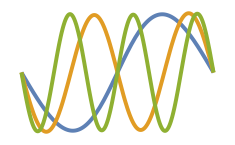

## Outline

I would like to discuss new features in the following areas:

Function Properties

Special Functions

Calculus

Online Courses

## Function Properties

### Set-Theoretical Properties

• FunctionInjective

• FunctionSurjective

• FunctionBijective

### Topological and Analytic Properties

• FunctionDiscontinuities

• FunctionSingularities

• FunctionContinuous

• FunctionAnalytic

• FunctionMeromorphic

### Sign Properties of Real Functions

• FunctionSign

• FunctionMonotonicity

• FunctionConvexity

## Function Properties—Example

Prove that tan^-1(x)+sin(x)/(2 x^2) has a limit for x→∞:

```mathematica
f=ArcTan[x]+Sin[x]/(2x^2);
```

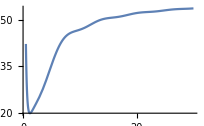

```mathematica
Plot[f,{x,1/2,30},PlotRange->All]
```

f is nondecreasing and bounded from above for x≥2:

```mathematica
{FunctionMonotonicity[{f,x≥2},x], FunctionSign[{2-f,x≥2},x]}
```

{1,1}

The limit of f at ∞ equals the supremum of f:

```mathematica
{Limit[f,x->∞],MaxValue[{f,x≥2},x]}
```

{π/2,π/2}

## Singularities of Functions

FunctionSingularities computes the singularities of functions.

For example, consider the following function f:

```mathematica
Clear[f]
```

```mathematica
f[p_]:=ArcTan[p^2]
```

### Real Singularities

The function f has no singularities for real values of x:

```mathematica
FunctionSingularities[f[x],x]
```

False

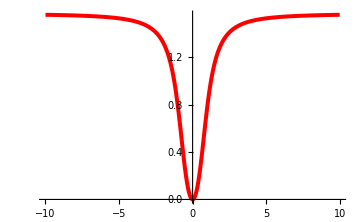

```mathematica
Plot[f[x], {x, -10, 10}, PlotRange -> All,ImageSize->Medium,PlotStyle->{Thickness[0.008],Red}]
```

### Complex Singularities

Find the singularities of the function in the complex plane:

```mathematica
FunctionSingularities[f[z],z,Complexes]
```

-ⅈ+z^2==0||ⅈ+z^2==0||(Re[z^2]==0&&Im[z^2]≥1)||(Re[z^2]==0&&Im[z^2]≤-1)

Compute the singularities in terms of Re[z] and Im[z]:

```mathematica
Reduce[%,z]
```

(Re[z]≤-1/(√2)&&(Im[z]==Re[z]||Im[z]==-Re[z]))||(Re[z]≥1/(√2)&&(Im[z]==-Re[z]||Im[z]==Re[z]))

Visualize the singularities:

```mathematica
Show[{ComplexPlot[f[z],{z,-2-2I,2+2I}],Region[Style[ImplicitRegion[%,{{Re[z],-2,2},{Im[z],-2,2}}],Red]]}]
```

-Graphics-

## Jacobian Elliptic Functions

There are 12 Jacobian elliptic functions (JacobiSN, JacobiCN, etc.).

Similarly, there are 12 inverse Jacobian elliptic functions (InverseJacobiSN etc.).

### Real Line

The Jacobian elliptic functions are periodic and analytic on the real line:

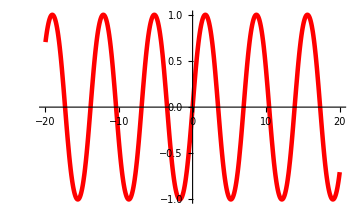

```mathematica
Plot[JacobiSN[x, 1/3], {x, -20, 20},ImageSize->Medium,PlotStyle->{Thickness[0.009],Red}]
```

```mathematica
{FunctionAnalytic[JacobiSN[x, 1/3],x],FunctionPeriod[JacobiSN[x, 1/3],x]}
```

{True,4 EllipticK[1/3]}

### Complex Plane

The Jacobian elliptic functions are doubly periodic and meromorphic in the complex plane:

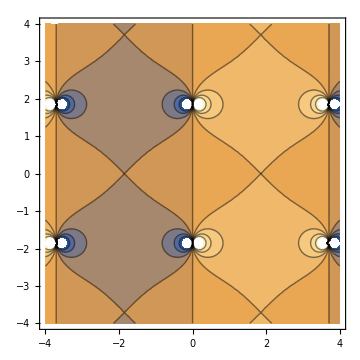

```mathematica
ContourPlot[Re[JacobiSN[x+ⅈ y,1/2]],{x,-4,4},{y,-4,4},ImageSize->Medium]
```

```mathematica
{FunctionMeromorphic[JacobiSN[x, 1/3],x],FunctionPeriod[JacobiSN[x, 1/3],x,Complexes]}
```

{True,{4 EllipticK[1/3],2 ⅈ EllipticK[2/3]}}

## JacobiEpsilon and JacobiZN

Two new functions, JacobiEpsilon and JacobiZN, have been implemented for Version 12.2.

JacobiEpsilon is defined to be the integral of the square of JacobiDN:

```mathematica
∫_0^u JacobiDN[z,k]^2 ⅆz
```

JacobiEpsilon[u,k]

JacobiZN is a meromorphic extension of JacobiZeta:

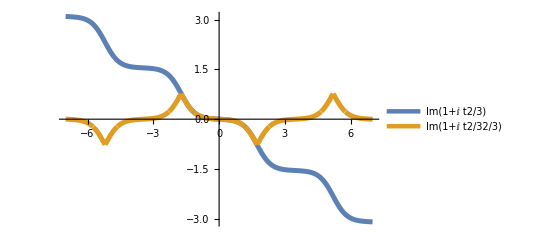

```mathematica
With[{m=2/3, u=1+I t},Plot[{Im[JacobiZN[u,m]],Im[JacobiZeta[JacobiAmplitude[u,m],m]]},{t,-7,7},PlotLegends->"Expressions",PlotStyle->Thickness[0.009]]]
```

## Lamé Functions

LameC and LameS, along with their associated functions, have been implemented in Version 12.2.

Each function solves a linear second-order ODE with elliptic coefficients:

```mathematica
DSolve[y''[x]+(LameEigenvalueB[ν,j,m]-ν (ν+1) m JacobiSN[x,m]^2)y[x] ==0,y[x],x]
```

{{y[x]→C[1] LameS[ν,j,x,m]+C[2] LameS[ν,j,x,m] 1/LameS[ν,j,K[1],m]^2K[1]1x}}

The Lamé functions include trigonometric functions as special cases:

```mathematica
{LameS[ν,1,z,0],LameS[ν,4,z,0]}//Simplify
```

{Cos[z],-Sin[4 z]}

Plot the first three even LameS functions:

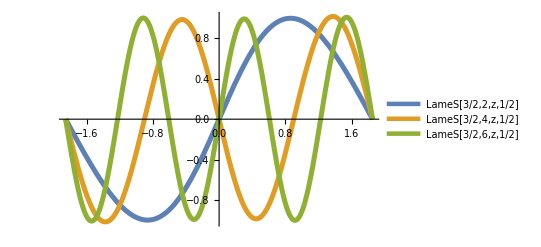

```mathematica
With[{ν=3/2,m=1/2},
Plot[{LameS[ν,2,z,m],LameS[ν,4,z,m],LameS[ν,6,z,m]},{z,-EllipticK[m],EllipticK[m]},Evaluated->True,PlotLegends->"Expressions",PlotStyle->Thickness[0.009]]]
```

The Lamé functions can be used to solve the Helmholtz equation in spheroconal coordinates.

## Holonomic Functions

DifferentialRoot and DifferenceRoot have new typesetting, improved documentation, etc. in Version 12.2.

For example, define a object f:

```mathematica
f=DifferentialRoot[Function[{y,x},{y''[x]+x^2 y'[x]+y[x]==0,y[0]==0,y'[0]==2}]]
```

Plot f:

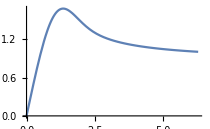

```mathematica
Plot[f[x],{x,0,2π}]
```

Compute an asymptotic expansion for f:

```mathematica
Asymptotic[f[x],{x,0,10}]
```

2 x-x^3/3-x^4/6+x^5/60+(7 x^6)/180+(13 x^7)/840-(11 x^8)/5040-(209 x^9)/60480-(107 x^10)/90720

DifferentialRoot and DifferenceRoot are expected to play a role similar to Root in calculus.

## Laplace Transforms

The Laplace transform of a function f is defined to be ∫_0^∞ f(t) ⅇ^(-s t)ⅆt.

The Laplace transform is an analytic function of s in a complex half-plane:

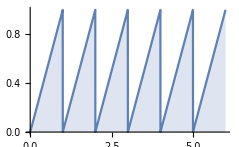

```mathematica
Plot[SawtoothWave[t],{t,0,6},Exclusions->None,Filling->Axis]
```

```mathematica
LaplaceTransform[SawtoothWave[t],t,s]//Together
```

(-1+ⅇ^s-s)/((-1+ⅇ^s) s^2)

Version 12.2 provides the inversion of such transforms using the Bromwich contour integral method.

It is also adds support for numerical inversion of Laplace transforms using a variety of methods.

Finally, it includes improved documentation for LaplaceTransform and InverseLaplaceTransform.

## Symbolic Inversion of Laplace Transforms

The following example is evaluated using the Bromwich contour integral method in Version 12.2:

```mathematica
InverseLaplaceTransform[1/(s Sinh[3s]),s,t]
```

t/3+(Piecewise[{{-(ⅈ ⅇ^(1/3 ⅈ n π (3+t)))/(n π), n≠0}, {0, True}}])n-∞∞

```mathematica
Activate[%]
```

t/3-(ⅈ (-Log[1+ⅇ^((ⅈ π t)/3)]+Log[ⅇ^(-1/3 ⅈ π t) (1+ⅇ^((ⅈ π t)/3))]))/π

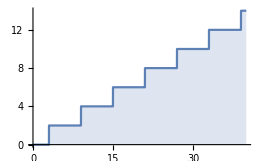

```mathematica
Plot[%,{t,0,40},Exclusions->None,Filling->Axis]
```

## Numerical Inversion of Laplace Transforms

Version 12.2 provides modern algorithms for numerical inversion of Laplace transforms.

For example, compare the numerical and symbolic inverses for a function:

```mathematica
g[t_?NumericQ]:=InverseLaplaceTransform[Sqrt[s]/(1+s^2),s,t]
```

```mathematica
g[1.3]
```

0.766095

```mathematica
InverseLaplaceTransform[Sqrt[s]/(1+s^2),s,t]
```

√2 (Cos[t] FresnelC[√(2/π) √t]+FresnelS[√(2/π) √t] Sin[t])

```mathematica
%/.{t->1.3}
```

0.766095

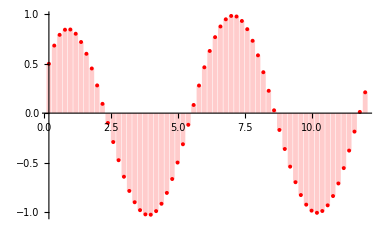

```mathematica
DiscretePlot[g[t],{t,0,12,0.2},PlotRange-> All,PlotStyle->{Thickness[0.009],Red}]
```

## Ordinary Differential Equations

Version 12.2 includes several improvements for exact solutions of linear and nonlinear ODEs.

For example, DSolve now returns a solution for the normal forms of Heun ODEs:

```mathematica
DSolveValue[y''[x]+(a x^4+b x^3+c x^2+d x+e)/x^4 y[x]==0,y[x],x]
```

ⅇ^(-(ⅈ √e)/x+ⅈ √a x) x^(1+(ⅈ d)/(2 √e)) C[2] HeunD[(d^2-2 ⅈ d √e-4 c e+8 √a e^(3/2))/(4 e),b+√a (2 ⅈ-d/(√e)),2 ⅈ √e,2+(ⅈ d)/(√e),2 ⅈ √a,x]+ⅇ^((ⅈ √e)/x-ⅈ √a x) x^(1-(ⅈ d)/(2 √e)) C[1] HeunD[(d^2+2 ⅈ d √e-4 c e+8 √a e^(3/2))/(4 e),b+√a (-2 ⅈ-d/(√e)),-2 ⅈ √e,2-(ⅈ d)/(√e),-2 ⅈ √a,x]

DSolve can now solve essentially every solvable ODE from the collection in the book by Kamke (1959).

## Partial Differential Equations

Version 12.2 includes substantial improvements for exact solutions of linear PDEs.

For example, DSolve can now solve the heat equation in cylindrical coordinates:

```mathematica
DSolve[{r Derivative[0,0,1][u][r,z,t]==1/50 r Derivative[0,2,0][u][r,z,t]+1/50 Derivative[1,0,0][u][r,z,t]+1/50 r Derivative[2,0,0][u][r,z,t],u[r,z,0]==(1-r)^2 (2-z)^2 z^3,Derivative[1,0,0][u][1,z,t]==0,Derivative[0,1,0][u][r,0,t]==0,Derivative[0,1,0][u][r,2,t]==0},u[r,z,t],{r,z,t}];
```

The following shows a time slice of the solution:

-Graphics3D-

Also, a monograph on symbolic solutions of PDEs using DSolve is under preparation.

## Asymptotic Statistics

Version 12.2 introduces AsymptoticProbability and AsymptoticExpectation for asymptotic statistics.

These functions are the asymptotic versions of Probability and Expectation.

For example, compare the asymptotic MGFs for the binomial and normal distributions:

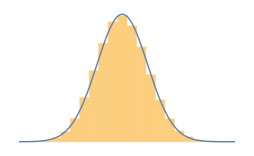

```mathematica
a1=AsymptoticExpectation[ⅇ^(t x),x\[Distributed]BinomialDistribution[n,p],{t,0,7}];
```

```mathematica
a2=AsymptoticExpectation[ⅇ^(t x),x\[Distributed]NormalDistribution[n p,√(n p (1-p))],{t,0,7}];
```

```mathematica
a1/.{n->30.,p->0.3}
```

1+9. t+43.65 t^2+150.27 t^3+409.623 t^4+937.138 t^5+1865.14 t^6+3308.34 t^7

```mathematica
a2/.{n->30.,p->0.3}
```

1+9. t+43.65 t^2+149.85 t^3+405.911 t^4+919.451 t^5+1805.38 t^6+3148.71 t^7

## Mathematics Courses

The online Wolfram U™ Linear Algebrahttps://www.wolfram.com/wolfram-u/introduction-to-linear-algebra/Nonehttps://www.wolfram.com/wolfram-u/introduction-to-linear-algebra/HyperlinkActionRecycledHyperlinkActive course was released during August 2020.

-Graphics-

A new course on differential equations is scheduled for release during Spring/Summer 2021.

Also, a course on elementary algebra, including applications to Optimization etc. is under development.

## Conclusion

Version 12.2 includes a wide variety of new mathematics features for users at all levels.

The new functionality will provide the basis for future developments in this area.

We also expect to continue working on new documentation examples and online courses.